```mathematica
dir=NotebookDirectory[];
a=SetDirectory[dir]
date = DateString[Riffle[{"Month","Day"},"_"]]
```

D:\Curve Elasticity\Simulation\2026\jan\results\SphereC\4at3

01_30

```mathematica
gb=1;
X[u_,v_]:=gb*{Sin[u] Cos[v],Sin[u] Sin[v],Cos[u]};

uu=Import["uu_4_26_"<>date<>".txt","Table"];
vv=Import["vv_4_26_"<>date<>".txt","Table"];
uu=Flatten[uu];
vv=Flatten[vv];
points=MapThread[X,{uu,vv}];
V2k=Graphics3D[{Yellow,Thick,Line[points]},Boxed->False];

V3=ParametricPlot3D[X[u,v],{u,0,Pi},{v,0,2Pi},PlotStyle->Directive[LightRed]];

Show[ V3,V2k,PlotRange->All]
Show[ V2k,PlotRange->All];
```

-Graphics3D-

```mathematica
Pi/4//N
```

0.785398

0.57735

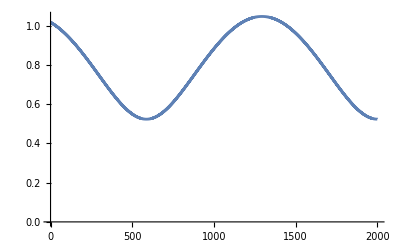

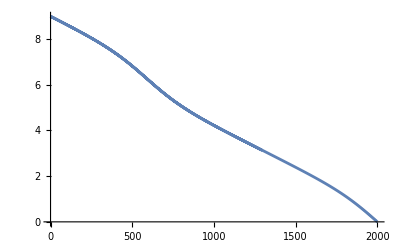

```mathematica
ListLinePlot[Transpose[uu],PlotRange->All]
ListLinePlot[Transpose[vv],PlotRange->All]
```

```mathematica
l1=Import["D:\\Curve Elasticity\\Simulation\\oct\\oct13\\sphere\\4at3\\l1_4_25_10_13.txt","Table"] //Flatten;

l2=Import["D:\\Curve Elasticity\\Simulation\\oct\\oct13\\sphere\\4at3\\l2_4_25_10_13.txt","Table"] //Flatten;

ListLinePlot[Transpose[l1],PlotRange->All]
ListLinePlot[Transpose[l2],PlotRange->All]
```

Import::nffil: File D:\Curve Elasticity\Simulation\oct\oct13\sphere\4at3\l1_4_25_10_13.txt not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File D:\Curve Elasticity\Simulation\oct\oct13\sphere\4at3\l2_4_25_10_13.txt not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

ListLinePlot::lpn: Transpose[Flatten[$Failed]] is not a list of numbers or pairs of numbers.

ListLinePlot[Transpose[Flatten[$Failed]],PlotRange→All]

ListLinePlot::lpn: Transpose[Flatten[$Failed]] is not a list of numbers or pairs of numbers.

ListLinePlot[Transpose[Flatten[$Failed]],PlotRange→All]

```mathematica
X[u_,v_]:={Sin[u] Cos[v],Sin[u] Sin[v],Cos[u]};
(*First derivatives*)
Xu=D[X[u,v],u]
Xv=D[X[u,v],v]

(*Second derivatives*)
Xuu=D[X[u,v],{u,2}];
Xuv=D[Xu,v];
Xvv=D[X[u,v],{v,2}];

(*Normal vector to surface*)
nVec=Cross[Xv,Xu]//Simplify 
n2=Sqrt[nVec.nVec]  //FullSimplify ;
n2=Sin[u];
nVec=nVec/n2 //FullSimplify;

(*First fundamental form:g_ij= <X_i,X_j>*)
g11=Simplify[Xu.Xu];
g12=Simplify[Xu.Xv];
g22=Simplify[Xv.Xv];
gMat={{g11,g12},{g12,g22}}


(*Second fundamental form:b_ij= <X_ij,n>*)
b11=Simplify[Xuu.nVec];
b12=Simplify[Xuv.nVec];
b22=Simplify[Xvv.nVec];
bMat={{b11,b12},{b12,b22}}
```

{Cos[u] Cos[v],Cos[u] Sin[v],-Sin[u]}

{-Sin[u] Sin[v],Cos[v] Sin[u],0}

{-Cos[v] Sin[u]^2,-Sin[u]^2 Sin[v],-Cos[u] Sin[u]}

{{1,0},{0,Sin[u]^2}}

{{1,0},{0,Sin[u]^2}}

```mathematica
ChristoffelSymbol[g_,xx_]:=Block[{n,ig,res},n=Length[xx];ig=Inverse[g];res=Table[(1/2)*Sum[ig[[i,s]]*(-D[g[[j,k]],xx[[s]]]+D[g[[j,s]],xx[[k]]]+D[g[[s,k]],xx[[j]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}];Simplify[res]];

(*The coordinates*)xx={u,v};
CS=ChristoffelSymbol[gMat,xx]
```

{{{0,0},{0,-Cos[u] Sin[u]}},{{0,Cot[u]},{Cot[u],0}}}

```mathematica
X[u_,v_]:=gb*{Sin[u] Cos[v],Sin[u] Sin[v],Cos[u]};
NN= nVec ;
X0 = X[ Pi/3,x];
X01 = D[X0,x] ;
g1=Sqrt[X01.X01] //Simplify;
Xs=X01/g1;
Xss = D[Xs,x]/g1;
nn=Cross[NN,Xs] //Simplify;

ns=D[nn,x]/g1;
kg=Xss.nn  //Simplify  
kn = Xss.NN //Simplify  
taug = ns.NN //Simplify
```

(8 Cos[u])/(√3)

-(8 Cos[v-x] Sin[u])/(√3)

0

```mathematica
th = Pi/3 //N
kb = 1/(Sin[th]) //N
kgb = kb Cos[th] //N
kg = Cot[th] //N

(kg-kgb);
0-kgb;
```

1.0472

1.1547

0.57735

0.57735

```mathematica
NumberForm[th,16]
```

1.047197551196598

```mathematica
NumberForm[kb,16]
```

1.154700538379252

```mathematica
NumberForm[kgb,16]
```

0.577350269189626

```mathematica
NumberForm[kb,16]
```

1.154700538379252

```mathematica
N[2/(√3)]
```

1.1547

```mathematica
NumberForm[1.1547005383792517,16]
```

1.154700538379252

```mathematica
NumberForm[1.1808719834468142,16]
```

1.180871983446814

```mathematica
NumberForm[1.1883951057781212,16]
```

1.188395105778121